```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.0001,1,0]],B:=Inverse[β[ω,0.0001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,8000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
ListLinePlot[Table[tr[ω,0.0001,1,0],{ω,0,4,0.01}]]
```

```mathematica
m5[ω_,ϵ1_,ϵ2_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ2]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ2]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ2]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ2]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ2]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ2]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ2]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp11,imp,imp,imp,imp2,imp8,imp5,imp1,imp,imp,imp,imp10,imp3,imp,imp,imp14,imp6,imp7,imp,imp7,imp,imp4,imp,imp,imp,imp,imp,imp,imp,imp3,imp8,imp3,imp8,imp,imp,imp,imp1,imp10,imp1,imp12,imp12,imp11,imp,imp,imp13,imp,imp,imp6,imp,imp9,imp,imp2,imp,imp10,imp14,imp,imp,imp,imp9,imp,imp13,imp,imp,imp14,imp,imp6,imp4,imp,imp12,imp,imp,imp,imp,imp5,imp,imp,imp,imp11,imp,imp,imp7,imp,imp,imp4,imp,imp,imp,imp,imp,imp,imp5,imp,imp,imp,imp,imp13,imp9,imp,imp,imp2}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
If[tra1>3,3,tra1]]
```

```mathematica
m5[1.5,0.3,0.9]
```

0.733091

```mathematica
Table[{ω,Mean[Table[m5[ω,0.3,0.9],2000]]},{ω,Range[0,1.5,0.01]}]
```

{{0.,0.0000289223},{0.01,0.0000130006},{0.02,0.0000187139},{0.03,0.0000252604},{0.04,0.00004691},{0.05,0.0000678792},{0.06,0.0000940455},{0.07,0.000153562},{0.08,0.000186943},{0.09,0.000242613},{0.1,0.000313442},{0.11,0.000392874},{0.12,0.000505103},{0.13,0.000663041},{0.14,0.000759869},{0.15,0.0011178},{0.16,0.00134453},{0.17,0.00171972},{0.18,0.0020538},{0.19,0.00297565},{0.2,0.00446545},{0.21,0.00590203},{0.22,0.0100873},{0.23,0.0218079},{0.24,0.0902401},{0.25,0.152828},{0.26,0.209686},{0.27,0.271794},{0.28,0.330956},{0.29,0.380363},{0.3,0.414205},{0.31,0.447218},{0.32,0.471613},{0.33,0.487312},{0.34,0.507654},{0.35,0.530921},{0.36,0.530787},{0.37,0.536746},{0.38,0.535954},{0.39,0.547746},{0.4,0.526973},{0.41,0.49969},{0.42,0.881522},{0.43,1.21817},{0.44,0.90116},{0.45,0.714092},{0.46,0.632762},{0.47,0.59849},{0.48,0.589207},{0.49,0.615568},{0.5,0.629686},{0.51,0.664383},{0.52,0.679366},{0.53,0.704991},{0.54,0.740891},{0.55,0.783044},{0.56,0.788398},{0.57,0.822087},{0.58,0.849378},{0.59,0.839662},{0.6,0.870794},{0.61,0.914476},{0.62,0.920491},{0.63,0.919393},{0.64,0.970114},{0.65,0.955984},{0.66,0.976513},{0.67,1.00885},{0.68,1.01208},{0.69,1.0315},{0.7,1.05051},{0.71,1.05005},{0.72,1.05296},{0.73,1.06581},{0.74,1.11043},{0.75,1.09499},{0.76,1.09977},{0.77,1.1125},{0.78,1.13566},{0.79,1.13519},{0.8,1.16476},{0.81,1.16125},{0.82,1.15428},{0.83,1.15629},{0.84,1.08905},{0.85,1.01416},{0.86,1.18682},{0.87,0.984805},{0.88,0.772475},{0.89,0.724478},{0.9,0.739648},{0.91,0.782062},{0.92,0.859296},{0.93,0.914973},{0.94,0.9635},{0.95,1.04141},{0.96,1.10314},{0.97,1.13306},{0.98,1.20684},{0.99,1.21748},{1.,1.25043},{1.01,1.39115},{1.02,1.27093},{1.03,0.795713},{1.04,0.367466},{1.05,0.57136},{1.06,0.643173},{1.07,0.559027},{1.08,0.447607},{1.09,0.364053},{1.1,0.336221},{1.11,0.333486},{1.12,0.347533},{1.13,0.342904},{1.14,0.322593},{1.15,0.34552},{1.16,0.337381},{1.17,0.35587},{1.18,0.37685},{1.19,0.392215},{1.2,0.410242},{1.21,0.444826},{1.22,0.464236},{1.23,0.513302},{1.24,0.493022},{1.25,0.526531},{1.26,0.562604},{1.27,0.548277},{1.28,0.579467},{1.29,0.552618},{1.3,0.588199},{1.31,0.609164},{1.32,0.58601},{1.33,0.638245},{1.34,0.594979},{1.35,0.639412},{1.36,0.648816},{1.37,0.65713},{1.38,0.678582},{1.39,0.630026},{1.4,0.646817},{1.41,0.665012},{1.42,0.63652},{1.43,0.661805},{1.44,0.672015},{1.45,0.606274},{1.46,0.560522},{1.47,0.622699},{1.48,0.613599},{1.49,0.622822},{1.5,0.63016}}

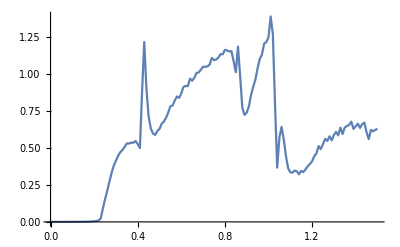

```mathematica
ListPlot[%52,Joined->True]
```

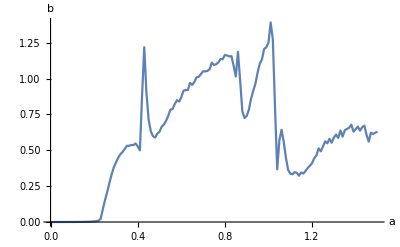

```mathematica
Show[%53,AxesLabel->{HoldForm[a],HoldForm[b]},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

```mathematica
Show[%53,AxesLabel->{HoldForm[a],HoldForm[b]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

-Graphics-

```mathematica
Export["na_7_nb_739.dat",%52]
```

na_7_nb_739.dat

```mathematica
[[ω*100+1]][[2]]
```

```mathematica
λ[ω_]:=Reverse[{Import["/home/shardulmukim/na_0_nb_1439.dat"][[ω*100+1]][[2]],Import["/home/shardulmukim/na_4_nb_1039.dat"][[ω*100+1]][[2]],Import["/home/shardulmukim/na_7_nb_739.dat"][[ω*100+1]][[2]],Import["/home/shardulmukim/na_10_nb_439.dat"][[ω*100+1]][[2]], Import["/home/shardulmukim/na_14_nb_039.dat"][[ω*100+1]][[2]],tr[ω,0.0001,1,0]}]
```

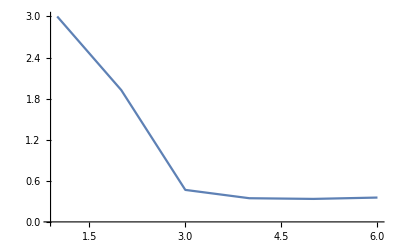

```mathematica
ListLinePlot[λ[1.15],PlotRange->All]
```

```mathematica
data=Flatten[Table[{x,y,x^2+y^2},{x,3,9},{y,2,10}],1]
```

{{3,2,13},{3,3,18},{3,4,25},{3,5,34},{3,6,45},{3,7,58},{3,8,73},{3,9,90},{3,10,109},{4,2,20},{4,3,25},{4,4,32},{4,5,41},{4,6,52},{4,7,65},{4,8,80},{4,9,97},{4,10,116},{5,2,29},{5,3,34},{5,4,41},{5,5,50},{5,6,61},{5,7,74},{5,8,89},{5,9,106},{5,10,125},{6,2,40},{6,3,45},{6,4,52},{6,5,61},{6,6,72},{6,7,85},{6,8,100},{6,9,117},{6,10,136},{7,2,53},{7,3,58},{7,4,65},{7,5,74},{7,6,85},{7,7,98},{7,8,113},{7,9,130},{7,10,149},{8,2,68},{8,3,73},{8,4,80},{8,5,89},{8,6,100},{8,7,113},{8,8,128},{8,9,145},{8,10,164},{9,2,85},{9,3,90},{9,4,97},{9,5,106},{9,6,117},{9,7,130},{9,8,145},{9,9,162},{9,10,181}}